```mathematica
(*Mathematica*)
```

```mathematica
(* bezier Mandelbrot Julia: as a Julia set on complex plane c point*)
```

```mathematica
Clear[f,g0,g,v]
```

```mathematica
f[z_,i_]=z^2+(0.1414234708212833+0.5836690226625129 ⅈ)*(i/30)+(1-i/30)*(0.08330262831549021+0.6113239202856731 ⅈ)
```

(0.0833026+0.611324 ⅈ) (1-i/30)+(0.00471412+0.0194556 ⅈ) i+z^2

```mathematica
(*{10.,51.334196},{25.,48.117839},{27.,50.052293},{30.,50.085535}*)
```

```mathematica
f[z,10]
```

(0.102676+0.602106 ⅈ)+z^2

```mathematica
Norm[(0.1026762424840879+0.602105621077953 ⅈ)]
```

0.610798

```mathematica
f[z,20]
```

(0.12205+0.592887 ⅈ)+z^2

```mathematica
f[z,25]
```

(0.131737+0.588278 ⅈ)+z^2

```mathematica
f[z,30]
```

(0.141423+0.583669 ⅈ)+z^2

```mathematica
g1=Flatten[ParallelTable[{i,Timing[JuliaSetPlot[f[z,i],z,Method -> "OrbitDetection",ColorFunction->Hue,ImageSize->{1920,1080},PlotStyle->{Opacity[0.2],Red,PointSize[0.0005]},AspectRatio->1,ImageResolution->1920,PerformanceGoal->"Quality","Bound"->32,Frame->False,Axes->False]][[1]]},{i,-40,70}]];
```

```mathematica
Length[g1]
```

222

```mathematica
g1
```

{-40,34.7513,-39,35.9431,-38,35.8674,-37,33.9095,-36,35.6016,-35,33.433,-34,34.2405,-33,34.488,-32,36.8858,-31,36.8799,-30,33.9378,-29,34.0304,-28,33.4664,-27,38.792,-26,35.5987,-25,36.9226,-24,32.9996,-23,33.7659,-22,34.7474,-21,37.8466,-20,33.6653,-19,35.3235,-18,31.7813,-17,31.9208,-16,31.7415,-15,32.2136,-14,34.6462,-13,33.5202,-12,39.1958,-11,40.9812,-10,39.5387,-9,39.899,-8,37.7697,-7,39.0237,-6,42.7239,-5,42.9424,-4,36.3853,-3,39.385,-2,41.1493,-1,42.4324,0,40.0524,1,37.8366,2,32.731,3,33.3043,4,44.9401,5,35.6116,6,45.1784,7,40.8232,8,36.7458,9,41.5407,10,51.3342,11,43.0371,12,35.7174,13,45.765,14,35.1949,15,35.3214,16,37.0474,17,32.2599,18,33.9084,19,39.725,20,35.5313,21,41.6403,22,43.3467,23,44.6804,24,43.9304,25,48.1178,26,39.1524,27,50.0523,28,38.0378,29,44.7004,30,50.0855,31,44.9788,32,45.121,33,43.179,34,41.0476,35,42.0448,36,42.3013,37,40.5379,38,38.9813,39,42.6974,40,40.8697,41,39.0207,42,37.3425,43,38.5495,44,42.0787,45,39.9224,46,38.6563,47,36.9313,48,39.6395,49,39.1361,50,42.8646,51,40.2915,52,39.3137,53,41.2426,54,39.5262,55,37.3928,56,36.2701,57,36.5013,58,36.6333,59,36.1628,60,37.5111,61,38.0245,62,41.2731,63,41.3159,64,37.7862,65,38.0766,66,37.9408,67,38.6894,68,37.3724,69,37.0768,70,32.8751}

```mathematica
gg=Table[N[{g1[[i]],g1[[i+1]]}],{i,1,Length[g1]-1,2}]
```

{{-40.,34.7513},{-39.,35.9431},{-38.,35.8674},{-37.,33.9095},{-36.,35.6016},{-35.,33.433},{-34.,34.2405},{-33.,34.488},{-32.,36.8858},{-31.,36.8799},{-30.,33.9378},{-29.,34.0304},{-28.,33.4664},{-27.,38.792},{-26.,35.5987},{-25.,36.9226},{-24.,32.9996},{-23.,33.7659},{-22.,34.7474},{-21.,37.8466},{-20.,33.6653},{-19.,35.3235},{-18.,31.7813},{-17.,31.9208},{-16.,31.7415},{-15.,32.2136},{-14.,34.6462},{-13.,33.5202},{-12.,39.1958},{-11.,40.9812},{-10.,39.5387},{-9.,39.899},{-8.,37.7697},{-7.,39.0237},{-6.,42.7239},{-5.,42.9424},{-4.,36.3853},{-3.,39.385},{-2.,41.1493},{-1.,42.4324},{0.,40.0524},{1.,37.8366},{2.,32.731},{3.,33.3043},{4.,44.9401},{5.,35.6116},{6.,45.1784},{7.,40.8232},{8.,36.7458},{9.,41.5407},{10.,51.3342},{11.,43.0371},{12.,35.7174},{13.,45.765},{14.,35.1949},{15.,35.3214},{16.,37.0474},{17.,32.2599},{18.,33.9084},{19.,39.725},{20.,35.5313},{21.,41.6403},{22.,43.3467},{23.,44.6804},{24.,43.9304},{25.,48.1178},{26.,39.1524},{27.,50.0523},{28.,38.0378},{29.,44.7004},{30.,50.0855},{31.,44.9788},{32.,45.121},{33.,43.179},{34.,41.0476},{35.,42.0448},{36.,42.3013},{37.,40.5379},{38.,38.9813},{39.,42.6974},{40.,40.8697},{41.,39.0207},{42.,37.3425},{43.,38.5495},{44.,42.0787},{45.,39.9224},{46.,38.6563},{47.,36.9313},{48.,39.6395},{49.,39.1361},{50.,42.8646},{51.,40.2915},{52.,39.3137},{53.,41.2426},{54.,39.5262},{55.,37.3928},{56.,36.2701},{57.,36.5013},{58.,36.6333},{59.,36.1628},{60.,37.5111},{61.,38.0245},{62.,41.2731},{63.,41.3159},{64.,37.7862},{65.,38.0766},{66.,37.9408},{67.,38.6894},{68.,37.3724},{69.,37.0768},{70.,32.8751}}

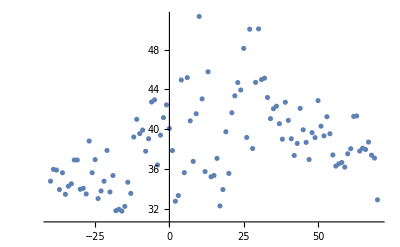

```mathematica
ListPlot[gg]
```

```mathematica
(*end*)
```

```mathematica
Clear[f]
```

```mathematica
(*Mathematica*)
```

```mathematica
f[z_]=(0.1026762424840879+0.602105621077953 ⅈ)+z^2
```

(0.102676+0.602106 ⅈ)+z^2

```mathematica
g1=JuliaSetPlot[f[z],z,Method -> "OrbitDetection",ColorFunction->Hue,ImageSize->{2000,2000},PlotStyle->{Opacity[0.2],Red,PointSize[0.0005]},AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality","Bound"->32,Frame->False,Axes->False]
```

```mathematica
v=JuliaSetPoints[f[z],z,"ClosenessTolerance"->0.001];
```

```mathematica
g2=ListPlot[v,ImageSize->2000,PlotStyle->{PointSize[0.001]},ColorFunction->Hue,PlotRange->All]
```

```mathematica
Export["Siegel_Disks_newbest_51p334196.jpg",{g1,g2}]
```

Siegel_Disks_newbest_51p334196.jpg

```mathematica
(*end*)
```

```mathematica
(* Mathematica*)
```

```mathematica
f[z_]=(0.1026762424840879+0.602105621077953 ⅈ)+z^2
```

(0.102676+0.602106 ⅈ)+z^2

#### 3D Mandelbrot/Julia

```mathematica
(*Mandelbrot/Julia with SQRT(x^2+y^2) limited measure*)
(*by R. L. BAGULA 18May2022 © *)
numberOfz2ToEscape[z_] := Block[
	{escapeCount, nz = N[z],nzold=0},
	For[
		escapeCount = 0,
		(Sqrt[Re[nz]^2+Im[nz]^2] < 128) && (escapeCount < 1024) && (Abs[nz-nzold]>10^(-3)),
		nzold=nz;
		nz=f[nz];
		++escapeCount
	];
	escapeCount*If[(Abs[nz-nzold]>10^(-3)),Abs[ArcTan[nz]+I*ArcTan[nz]*Tan[1]-Arg[z]],Abs[Arg[nz]]]
]
```

```mathematica
FractalPure[m_][{{ReMin_, ReMax_, ReSteps_},
			 {ImMin_, ImMax_, ImSteps_}}] :=
		ParallelTable[
			numberOfz2ToEscape[x + y I],
			{y, ImMin, ImMax, (ImMax - ImMin)/ImSteps},
			{x, ReMin, ReMax, (ReMax - ReMin)/ReSteps}
		
	]
```

```mathematica
arraym=FractalPure[m][{{-1.301,1.3001,1000},{-1.3001,1.3001,1000}}];
```

```mathematica
g1=ListPlot3D[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False,AspectRatio -> Automatic,Boxed->False, Axes->False,ColorFunction->Hue,Background->Black,ViewPoint->Above,ImageSize->2000];
```

```mathematica
g2=Rasterize[ListDensityPlot[Log[Abs[1/Max[arraym]+arraym-512/(arraym+Max[arraym])]],
                          Mesh -> False,
		                  AspectRatio -> Automatic,
		                ColorFunction-> (Hue[2#]&),ImageSize->2000,Frame->False],RasterSize->2000,ImageSize->2000];
```

```mathematica
colortab=Sort[Join[Flatten[Delete[Sort[Union[Table[Delete[Sort[Union[Flatten[Table[If[i+j+k==n,{(1)^2,(1-j)^2,(1-k)^2},{}],{i,0,1,1/10},{j,0,1,1/10},{k,0,1,1/10}],2]]],1],{n,0,1,1/30}]]],1],1],{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}},{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/2,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/1.5,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/3]];
```

```mathematica
Length[%]
```

542

```mathematica
cf[l_]:=Block[{niv,rgb},niv=If[l<1/542,1,Ceiling[542*l]];
rgb=colortab[[niv]];
RGBColor[rgb[[1]],rgb[[2]],rgb[[3]]]];
```

```mathematica
g3=Rasterize[ListDensityPlot[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False, AspectRatio -> Automatic, ColorFunction->cf,ImageSize->1000,Frame->False],RasterSize->2000,ImageSize->2000];
```

```mathematica
Export["j_1000_Siegel_Disks_newbest_51p334196_Out_In_Monitor.jpg",{g1,g2,g3}]
```

j_1000_Siegel_Disks_newbest_51p334196_Out_In_Monitor.jpg

```mathematica
(*end*)
```